```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

92

92

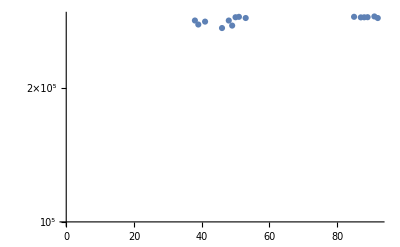

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{1*^5,All},
Joined->False
]
```

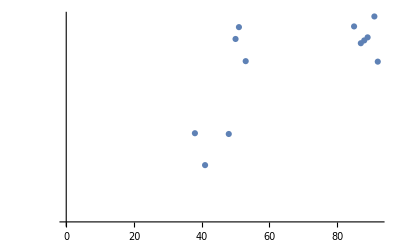

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{2.8*^5,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|S1EL_xOffset→0.0036169,S1EL_yOffset→0.000715137,S2EL_xOffset→-0.000161083,S2EL_yOffset→0.000191127,S2ER_xOffset→-0.000174903,S2ER_yOffset→0.00103933,S1ER_xOffset→0.0036623,S1ER_yOffset→0.00190711,Q5FFkG→-71.7389,Q4FFkG→-80.6071,Q3FFkG→99.5096,Q2FFkG→126.366,Q1FFkG→-234.802,Q0FFkG→126.359,XC1FFkG→0.250645,XC3FFkG→-0.132566,YC1FFkG→0.0105402,YC2FFkG→-0.0242936,PDrive_mean_x→4.3784×10^-6,PDrive_mean_y→3.7302×10^-6,PDrive_sigma_x→0.0000469522,PDrive_sigma_y→0.0000304847,PDrive_mean_xp→0.000496631,PDrive_mean_yp→0.0000612254,PDrive_median_x→4.4166×10^-6,PDrive_median_y→2.8367×10^-6,PDrive_median_xp→0.000541012,PDrive_median_yp→0.0000561794,PDrive_sigmaSI90_x→0.0000417385,PDrive_sigmaSI90_y→0.0000294054,PDrive_emitSI90_x→0.0000815524,PDrive_emitSI90_y→0.0000262775,PDrive_zLen→0.000019304,PDrive_zCentroid→991.332,PWitness_mean_x→-3.9316×10^-6,PWitness_mean_y→-4.462×10^-7,PWitness_sigma_x→0.0000261349,PWitness_sigma_y→0.0000271495,PWitness_mean_xp→0.000296227,PWitness_mean_yp→-4.0875×10^-6,PWitness_median_x→-3.2218×10^-6,PWitness_median_y→9.599×10^-7,PWitness_median_xp→0.000298273,PWitness_median_yp→-4.1988×10^-6,PWitness_sigmaSI90_x→0.0000241682,PWitness_sigmaSI90_y→0.0000243971,PWitness_emitSI90_x→0.0000158659,PWitness_emitSI90_y→4.6361×10^-6,PWitness_zLen→0.0000411588,PWitness_zCentroid→991.332,bunchSpacing→0.0000711442,transverseCentroidOffset→9.3005×10^-6,lostChargeFraction→0.,maximizeMe→290559.|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

S1EL_xOffset : 0.0036168975
S1EL_yOffset : 0.0007151365
S2EL_xOffset : -0.0001610827
S2EL_yOffset : 0.0001911273
S2ER_xOffset : -0.0001749033
S2ER_yOffset : 0.0010393349
S1ER_xOffset : 0.003662303
S1ER_yOffset : 0.0019071134
Q5FFkG : -71.7389156005
Q4FFkG : -80.607107854
Q3FFkG : 99.509554556
Q2FFkG : 126.365771721
Q1FFkG : -234.8016911618
Q0FFkG : 126.3593880842
XC1FFkG : 0.2506452436
XC3FFkG : -0.1325658033
YC1FFkG : 0.0105401835
YC2FFkG : -0.0242936317
PDrive_mean_x : 4.3784e-6
PDrive_mean_y : 3.7302e-6
PDrive_sigma_x : 0.0000469522
PDrive_sigma_y : 0.0000304847
PDrive_mean_xp : 0.0004966309
PDrive_mean_yp : 0.0000612254
PDrive_median_x : 4.4166e-6
PDrive_median_y : 2.8367e-6
PDrive_median_xp : 0.0005410119
PDrive_median_yp : 0.0000561794
PDrive_sigmaSI90_x : 0.0000417385
PDrive_sigmaSI90_y : 0.0000294054
PDrive_emitSI90_x : 0.0000815524
PDrive_emitSI90_y : 0.0000262775
PDrive_zLen : 0.000019304
PDrive_zCentroid : 991.3317376476
PWitness_mean_x : -3.9316e-6
PWitness_mean_y : -4.462e-7
PWitness_sigma_x : 0.0000261349
PWitness_sigma_y : 0.0000271495
PWitness_mean_xp : 0.0002962269
PWitness_mean_yp : -4.0875e-6
PWitness_median_x : -3.2218e-6
PWitness_median_y : 9.599e-7
PWitness_median_xp : 0.0002982731
PWitness_median_yp : -4.1988e-6
PWitness_sigmaSI90_x : 0.0000241682
PWitness_sigmaSI90_y : 0.0000243971
PWitness_emitSI90_x : 0.0000158659
PWitness_emitSI90_y : 4.6361e-6
PWitness_zLen : 0.0000411588
PWitness_zCentroid : 991.3318087917
bunchSpacing : 0.0000711442
transverseCentroidOffset : 9.3005e-6
lostChargeFraction : 0.
maximizeMe : 290558.7666184307

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

9.30045×10^-6

## Plot all

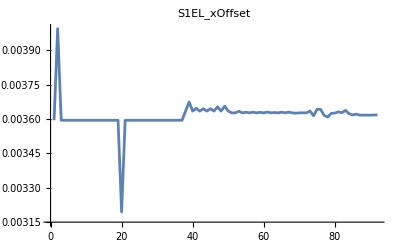
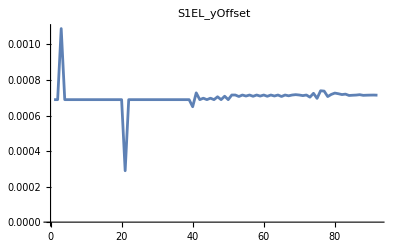
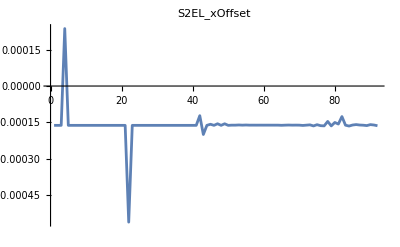
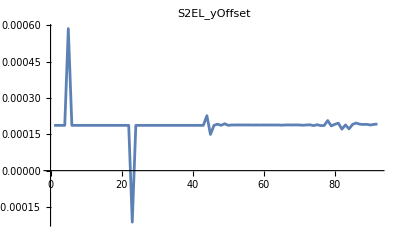
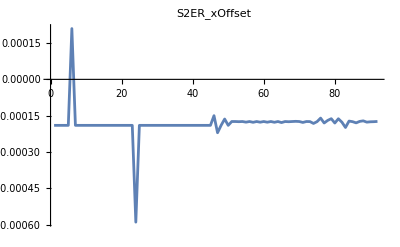
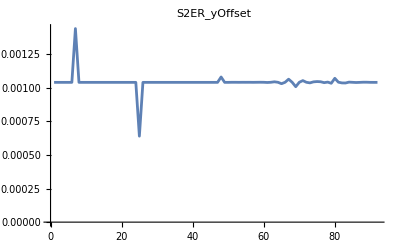
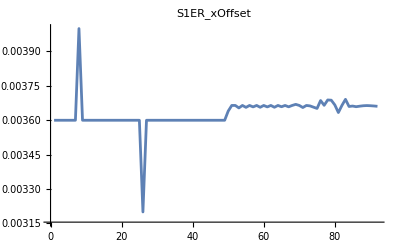
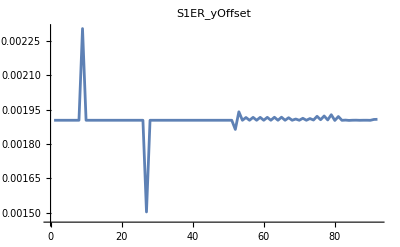
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

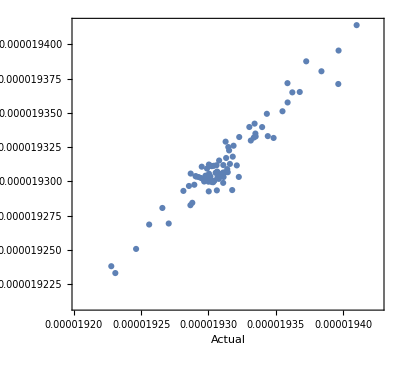

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVarsMathematica
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{Q0FFkG→Indeterminate,Q1FFkG→Indeterminate,Q2FFkG→Indeterminate,Q3FFkG→Indeterminate,Q4FFkG→Indeterminate,Q5FFkG→Indeterminate,S1ELxOffset→Indeterminate,S1ELyOffset→Indeterminate,S1ERxOffset→Indeterminate,S1ERyOffset→Indeterminate,S2ELxOffset→Indeterminate,S2ELyOffset→Indeterminate,S2ERxOffset→Indeterminate,S2ERyOffset→Indeterminate,XC1FFkG→Indeterminate,XC3FFkG→Indeterminate,YC1FFkG→Indeterminate,YC2FFkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
Q0FFkG | 1 | 2.38733×10^-17 | 2.38733×10^-17 | 0.058704 | 0.809236
Q1FFkG | 1 | 1.25988×10^-16 | 1.25988×10^-16 | 0.309804 | 0.579503
Q2FFkG | 1 | 3.14648×10^-15 | 3.14648×10^-15 | 7.73715 | 0.00687934
Q3FFkG | 1 | 2.56263×10^-14 | 2.56263×10^-14 | 63.0146 | 1.83994×10^-11
Q4FFkG | 1 | 1.36064×10^-14 | 1.36064×10^-14 | 33.458 | 1.68873×10^-7
Q5FFkG | 1 | 2.29414×10^-15 | 2.29414×10^-15 | 5.64126 | 0.0201708
S1ELxOffset | 1 | 1.49776×10^-13 | 1.49776×10^-13 | 368.298 | 3.05832×10^-30
S1ELyOffset | 1 | 7.59669×10^-17 | 7.59669×10^-17 | 0.186801 | 0.666866
S1ERxOffset | 1 | 1.02016×10^-13 | 1.02016×10^-13 | 250.856 | 2.54701×10^-25
S1ERyOffset | 1 | 1.73534×10^-15 | 1.73534×10^-15 | 4.26717 | 0.0424056
S2ELxOffset | 1 | 2.23471×10^-13 | 2.23471×10^-13 | 549.511 | 1.04718×10^-35
S2ELyOffset | 1 | 1.2164×10^-18 | 1.2164×10^-18 | 0.0029911 | 0.956534
S2ERxOffset | 1 | 1.34431×10^-12 | 1.34431×10^-12 | 3305.65 | 1.53315×10^-62
S2ERyOffset | 1 | 4.63769×10^-15 | 4.63769×10^-15 | 11.404 | 0.00117777
XC1FFkG | 1 | 8.02005×10^-15 | 8.02005×10^-15 | 19.7212 | 0.0000312494
XC3FFkG | 1 | 1.92551×10^-16 | 1.92551×10^-16 | 0.473479 | 0.493572
YC1FFkG | 1 | 3.01778×10^-15 | 3.01778×10^-15 | 7.42068 | 0.00806304
YC2FFkG | 1 | 1.28078×10^-15 | 1.28078×10^-15 | 3.14942 | 0.0801229
Error | 73 | 2.9687×10^-14 | 4.06672×10^-16 |  | 
Total | 91 | 1.91305×10^-12 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```